```mathematica
SetDirectory["~/GitHub/DIO_point_spec"]
```

/Users/robert/GitHub/DIO_point_spec

```mathematica
ExpandFileName["/Users/robert/GitHub/DIO_point_spec"]
```

/Users/robert/GitHub/DIO_point_spec

```mathematica
files10=FileNames["Zal.1*"]
files1=FileNames["Zal1*"]
```

{Zal.1_j0.dat,Zal.1_j10_k0.dat,Zal.1_j10_k-1.dat,Zal.1_j11_k0.dat,Zal.1_j11_k-1.dat,Zal.1_j12_k0.dat,Zal.1_j12_k-1.dat,Zal.1_j13_k0.dat,Zal.1_j13_k-1.dat,Zal.1_j14_k0.dat,Zal.1_j14_k-1.dat,Zal.1_j15_k0.dat,Zal.1_j15_k-1.dat,Zal.1_j16_k0.dat,Zal.1_j16_k-1.dat,Zal.1_j17_k0.dat,Zal.1_j17_k-1.dat,Zal.1_j18_k0.dat,Zal.1_j18_k-1.dat,Zal.1_j19_k0.dat,Zal.1_j19_k-1.dat,Zal.1_j1_k0.dat,Zal.1_j1_k-1.dat,Zal.1_j20_k0.dat,Zal.1_j20_k-1.dat,Zal.1_j21_k0.dat,Zal.1_j21_k-1.dat,Zal.1_j22_k0.dat,Zal.1_j22_k-1.dat,Zal.1_j23_k0.dat,Zal.1_j23_k-1.dat,Zal.1_j24_k0.dat,Zal.1_j24_k-1.dat,Zal.1_j25_k0.dat,Zal.1_j25_k-1.dat,Zal.1_j26_k0.dat,Zal.1_j26_k-1.dat,Zal.1_j27_k0.dat,Zal.1_j27_k-1.dat,Zal.1_j28_k0.dat,Zal.1_j28_k-1.dat,Zal.1_j29_k0.dat,Zal.1_j29_k-1.dat,Zal.1_j2_k0.dat,Zal.1_j2_k-1.dat,Zal.1_j30_k0.dat,Zal.1_j30_k-1.dat,Zal.1_j31_k0.dat,Zal.1_j31_k-1.dat,Zal.1_j3_k0.dat,Zal.1_j3_k-1.dat,Zal.1_j4_k0.dat,Zal.1_j4_k-1.dat,Zal.1_j5_k0.dat,Zal.1_j5_k-1.dat,Zal.1_j6_k0.dat,Zal.1_j6_k-1.dat,Zal.1_j7_k0.dat,Zal.1_j7_k-1.dat,Zal.1_j8_k0.dat,Zal.1_j8_k-1.dat,Zal.1_j9_k0.dat,Zal.1_j9_k-1.dat}

{Zal1_j0.dat,Zal1_j10_k0.dat,Zal1_j10_k-1.dat,Zal1_j11_k0.dat,Zal1_j11_k-1.dat,Zal1_j12_k0.dat,Zal1_j12_k-1.dat,Zal1_j13_k0.dat,Zal1_j13_k-1.dat,Zal1_j14_k0.dat,Zal1_j14_k-1.dat,Zal1_j15_k0.dat,Zal1_j15_k-1.dat,Zal1_j16_k0.dat,Zal1_j16_k-1.dat,Zal1_j17_k0.dat,Zal1_j17_k-1.dat,Zal1_j18_k0.dat,Zal1_j18_k-1.dat,Zal1_j19_k0.dat,Zal1_j19_k-1.dat,Zal1_j1_k0.dat,Zal1_j1_k-1.dat,Zal1_j20_k0.dat,Zal1_j20_k-1.dat,Zal1_j21_k0.dat,Zal1_j21_k-1.dat,Zal1_j22_k0.dat,Zal1_j22_k-1.dat,Zal1_j23_k0.dat,Zal1_j23_k-1.dat,Zal1_j24_k0.dat,Zal1_j24_k-1.dat,Zal1_j25_k0.dat,Zal1_j25_k-1.dat,Zal1_j26_k0.dat,Zal1_j26_k-1.dat,Zal1_j27_k0.dat,Zal1_j27_k-1.dat,Zal1_j28_k0.dat,Zal1_j28_k-1.dat,Zal1_j29_k0.dat,Zal1_j29_k-1.dat,Zal1_j2_k0.dat,Zal1_j2_k-1.dat,Zal1_j30_k0.dat,Zal1_j30_k-1.dat,Zal1_j31_k0.dat,Zal1_j31_k-1.dat,Zal1_j3_k0.dat,Zal1_j3_k-1.dat,Zal1_j4_k0.dat,Zal1_j4_k-1.dat,Zal1_j5_k0.dat,Zal1_j5_k-1.dat,Zal1_j6_k0.dat,Zal1_j6_k-1.dat,Zal1_j7_k0.dat,Zal1_j7_k-1.dat,Zal1_j8_k0.dat,Zal1_j8_k-1.dat,Zal1_j9_k0.dat,Zal1_j9_k-1.dat}

```mathematica
imax10=Length[files10]
imax1=Length[files1]
```

63

63

```mathematica
Clear[res10]
Do[res10[i]=Import[files10[[i]]]//ToExpression,{i,1,imax10}]
Clear[res1]
Do[res1[i]=Import[files1[[i]]]//ToExpression,{i,1,imax1}]
```

```mathematica
sum1=Table[{res1[1][[k,1]],Sum[res1[i][[k,2]],{i,1,imax1}]},{k,1,Length[res1[1]]}];
sum10=Table[{res10[1][[k,1]],Sum[res10[i][[k,2]],{i,1,imax10}]},{k,1,Length[res10[1]]}];
```

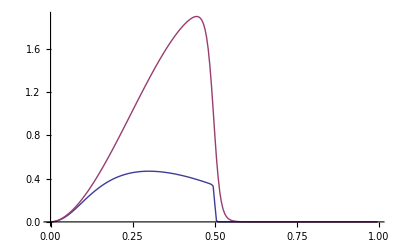

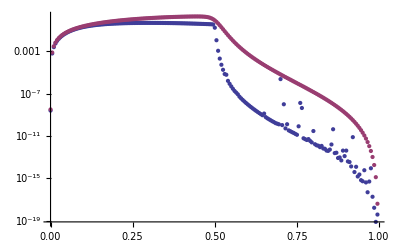

```mathematica
ListPlot[{sum1,sum10},Joined->True]
ListLogPlot[{sum1, sum10}]
```

```mathematica
NIntegrate[2Interpolation[sum1][x]//Chop,{x,0,Sqrt[1-(10/137)^2]}]
NIntegrate[2Interpolation[sum10][x],{x,10^-5,1-0.005}]
```

0.0240879

0.995891

```mathematica
1-Zal^2/2/.Zal->13/137.
1-Zal^2/.Zal->13/137.
```

0.995498

0.990996

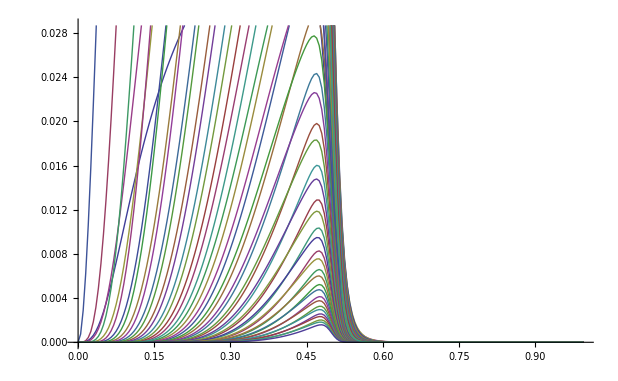

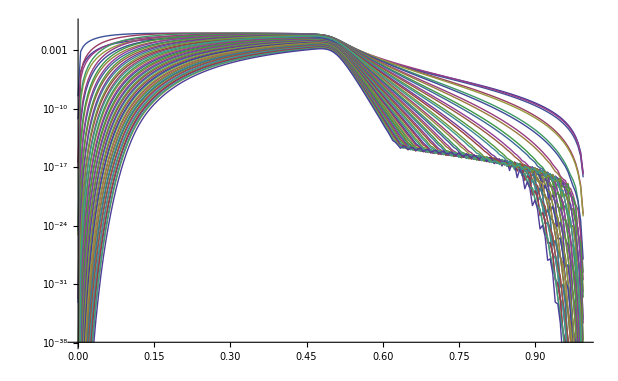

```mathematica
ListPlot[Table[res[i],{i,1,imax}], Joined->True]
ListLogPlot[Table[res[i],{i,1,imax}], Joined->True]
```

```mathematica
eexp=0.79(10/137)^5 1024/(5 Pi)(Sqrt[1-(10/137)^2]-i)^5
```

0.00010671 ((7 √381)/137-i)^5

```mathematica
tab=Table[{i,eexp},{i,0.95,1,0.001}];
```

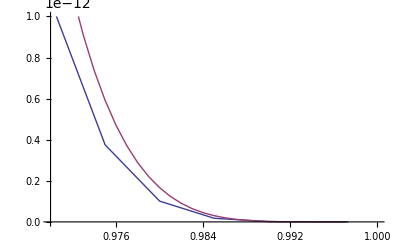

```mathematica
ListPlot[{sum,tab},PlotRange->{{0.97,1},{0,10^-12}},Joined->True]
```